```mathematica
fop=Internal`ProcessEquations`FirstOrderize[{-2 y[x]+4 y[x]^3+y''[x]-β D[y[x],{x,4}]==0},{x},1,{y}];
Column[fop,Dividers->All]
sys1o=Take[fop,2]//Flatten;(*first order system*)dvars=Through[Flatten[fop[[3]]][x]];(*dependent variables*)jac=D[(*Jacobian*)First@Values@Solve[sys1o,D[dvars,x]],{dvars}]
evals=Eigenvalues[jac]/.y[x]->y (*local EVs as func.of y and beta*)

Manipulate[Block[{β=b},Plot[{Evaluate@ReIm[evals]},{y,-0.8,0.8},MaxRecursion->10,  PlotLegends->"Expressions",   PlotRange->100000,PlotRangePadding->Scaled[.05],ScalingFunctions->{ArcTan,Tan},Frame->True, FrameTicks->{{{-1000,-5,-1,0,1,5,1000},Automatic},Automatic},FrameLabel->{y,HoldForm@ReIm@λ}]],Row[{Control@{{b,1/8,β},{1/32, 1/16,1/8, 1/4,1/2}}," ",Dynamic@Style[b,"Label"]}]]
```

{-2 y[x]+4 y[x]^3+NDSolve`y$39$1$2[x]-β NDSolve`y$39$1$2$3'[x]==0}
{y'[x]==NDSolve`y$39$1[x],NDSolve`y$39$1'[x]==NDSolve`y$39$1$2[x],NDSolve`y$39$1$2'[x]==NDSolve`y$39$1$2$3[x]}
{{y,NDSolve`y$39$1,NDSolve`y$39$1$2,NDSolve`y$39$1$2$3}}
{NDSolve`y$39$1→y',NDSolve`y$39$1$2→y'',NDSolve`y$39$1$2$3→y^(3)}

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{(-2+12 y[x]^2)/β,0,1/β,0}}

{-(√(β-β √(1-8 β+48 y^2 β)))/(√2 β),(√(β-β √(1-8 β+48 y^2 β)))/(√2 β),-(√(β+β √(1-8 β+48 y^2 β)))/(√2 β),(√(β+β √(1-8 β+48 y^2 β)))/(√2 β)}

```mathematica
fop0=Internal`ProcessEquations`FirstOrderize[{-2 y[x]+4 y[x]^3+y''[x]==0},{x},1,{y}];
Column[fop0,Dividers->All]
sys1o=Take[fop0,2]//Flatten;
```

{-2 y[x]+4 y[x]^3+NDSolve`y$40$1'[x]==0}
{y'[x]==NDSolve`y$40$1[x]}
{{y,NDSolve`y$40$1}}
{NDSolve`y$40$1→y'}

```mathematica
(*first order system*)dvars=Through[Flatten[fop0[[3]]][x]];
dvars;
First@Values@Solve[sys1o,D[dvars,x]]
```

{NDSolve`y$40$1[x],-2 (-y[x]+2 y[x]^3)}

```mathematica
(*dependent variables*)jac=D[(*Jacobian*)First@Values@Solve[sys1o,D[dvars,x]],{dvars}]
evals=Eigenvalues[jac]/.y[x]->y (*local EVs as func.of y and beta*)
jac
Re[evals]
```

{{0,1},{-2 (-1+6 y[x]^2),0}}

{-√2 √(1-6 y^2),√2 √(1-6 y^2)}

{{0,1},{-2 (-1+6 y[x]^2),0}}

{-√2 Re[√(1-6 y^2)],√2 Re[√(1-6 y^2)]}

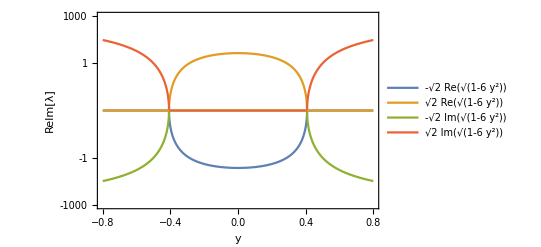

```mathematica
Plot[{Evaluate@{Re[evals],Im[evals]}},{y,-0.8,0.8},MaxRecursion->10,PlotRange->100000,PlotRangePadding->Scaled[.05],ScalingFunctions->{ArcTan,Tan},Frame->True,PlotLegends->"Expressions",  FrameTicks->{{{-1000,-5,-1,0,1,5,1000},Automatic},Automatic},FrameLabel->{y,HoldForm@ReIm@λ}]
```

```mathematica
lis = {y,y^2}
```

{y,y^2}

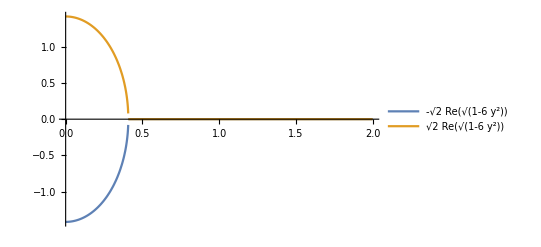

```mathematica
Plot[{Evaluate@Re[evals]},{y,0,2}, PlotLegends->"Expressions"]
```

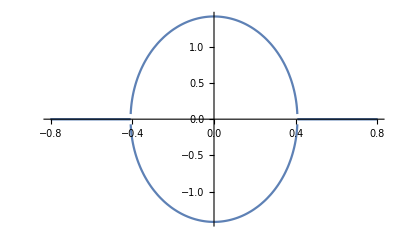

```mathematica
Plot[{Re[evals]},{y,-0.8,0.8}]
```

```mathematica
Re[evals]
```

{-√2 Re[√(1-6 y^2)],√2 Re[√(1-6 y^2)]}